## Settings

```mathematica
imgsize=700;
```

```mathematica
eqn = D[D[f[x],x],x]-( a k Cot[k x]+i(omegam - a Sin[k x]Cos[2thetam]) a Sin[k x] )D[f[x],x]+(Sin[2 thetam]/2)^2 a^2 Sin[k x]^2 f[x]==0
```

1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0

```mathematica
DSolve[eqn,f[x],x]
```

DSolve[1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0,f[x],x]

```mathematica
DSolve[f[x]+x D[f[x],x]==omegam/2-deltalambda[x]Sin[2thetam]/2,f[x],x]
```

{{f[x]→C[1]/x+(∫_1^x 1/2 (omegam-deltalambda[K[1]] Sin[2 thetam])ⅆK[1])/x}}

```mathematica
sys=I D[{phi1[x],phi2[x]},x]=={{0,(g0R+I g0I) Exp[I(-omegam+n0 k)x]},{(g0R-I g0I) Exp[-I(-omegam+n0 k)x],0}}.{phi1[x],phi2[x]}
```

{ⅈ phi1'[x],ⅈ phi2'[x]}=={ⅇ^(ⅈ (k n0-omegam) x) (ⅈ g0I+g0R) phi2[x],ⅇ^(-ⅈ (k n0-omegam) x) (-ⅈ g0I+g0R) phi1[x]}

```mathematica
DSolve[sys,{phi1,phi2},x]
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

```mathematica
%//FullSimplify
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

## Understand The Hamiltonian

```mathematica
ClearAll[k,x,phi,function1,constant1]
DSolve[I D[function1[x],x]==constant1 Sin[k x+phi]function1[x],function1,x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-ⅈ constant1 (-(Cos[phi] Cos[k x])/k+(Sin[phi] Sin[k x])/k)) C[1]]}}

```mathematica
ClearAll[a,k,x,phi,function1,constant1]
DSolve[D[D[function1[x],x],x]-D[a Sin[k x + phi],x]/(a Sin[k x + phi])D[function1[x],x]==-Sin[2thetam]^2/4(a Sin[k x + phi])^2 function1[x],function1,x]
```

{{function1→Function[{x},C[1] Cos[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]-C[2] Sin[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]]}}

## Constant Matter ‘Perturbation’

```mathematica
ClearAll[k,x,phi,function1,function2,constant1]
DSolve[I D[{function1[x],function2[x]},x]==Sin[2thetam]/2 lambdac{{0,Exp[I Cos[2thetam]lambdac x-I omegam x]},{Exp[-I Cos[2thetam]lambdac x + I omegam x],0}}.{function1[x],function2[x]},{function1,function2},x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1]+ⅇ^(1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2]],function2→Function[{x},1/lambdac ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1] (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]+1/lambdac ⅈ ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]+1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2] (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]]}}

## Investigate Resonance

Define the amplitude

```mathematica
ClearAll[khat,ahat,themtam,zk,n0,x,phi,function1,function2,constant1]
```

```mathematica
fun[khat_,ahat_,thetam_]=1/4 ahat Sin[2thetam](2n0+1)/zk BesselJ[n0,zk]/.{zk->ahat/khat Cos[2thetam],n0->Round[1/khat]}
```

1/4 khat BesselJ[Round[1/khat],(ahat Cos[2 thetam])/khat] (1+2 Round[1/khat]) Tan[2 thetam]

```mathematica
amplitude[khat_,ahat_,thetam_] = (4 Abs[fun[khat,ahat,thetam]]^2)/(4 Abs[fun[khat,ahat,thetam]]^2+(n0 khat - 1)^2)/.{zk->ahat/khat Cos[2thetam],n0->Round[1/khat]}
```

Abs[khat BesselJ[Round[1/khat],(ahat Cos[2 thetam])/khat] (1+2 Round[1/khat]) Tan[2 thetam]]^2/(4 (1/4 Abs[khat BesselJ[Round[1/khat],(ahat Cos[2 thetam])/khat] (1+2 Round[1/khat]) Tan[2 thetam]]^2+(-1+khat Round[1/khat])^2))

```mathematica
Limit[amplitude[k,a,t],k->Infinity]
```

1

```mathematica
Limit[amplitude[k,a,t],k->0]
```

Limit[Abs[k BesselJ[Round[1/k],(a Cos[2 t])/k] (1+2 Round[1/k]) Tan[2 t]]^2/(4 (1/4 Abs[k BesselJ[Round[1/k],(a Cos[2 t])/k] (1+2 Round[1/k]) Tan[2 t]]^2+(-1+k Round[1/k])^2)),k→0]

```mathematica
Limit[amplitude[k,a,t],a->0]
```

$Aborted

```mathematica
Limit[amplitude[k,a,t],t->0]
(*Limit[amplitude[k,a,t],t->Pi/4]*)
```

0

```mathematica
Table[{amplitude[k,0.1,Pi/5],k},{k,0.1,1,0.1}]
```

{1.,1.,5.40673×10^-7,0.000131646,1.,0.000058546,0.0534823,0.112806,0.33715,1.}

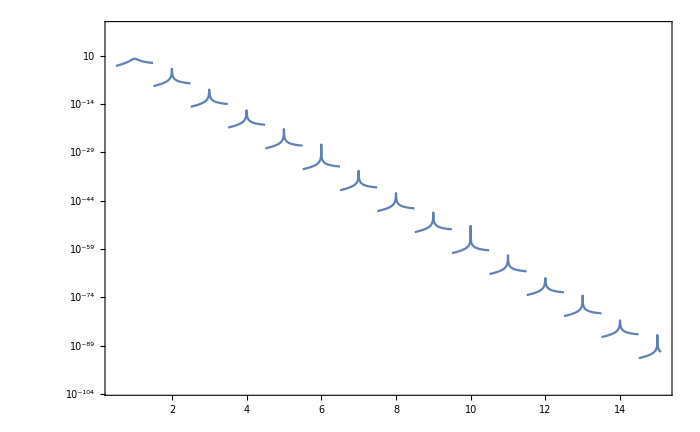

```mathematica
LogPlot[amplitude[1/k,0.1,Pi/4.01],{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->Automatic]
```

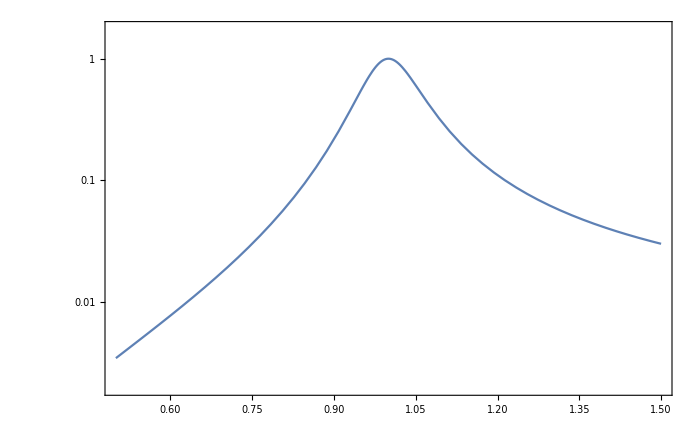

```mathematica
LogPlot[amplitude[1/k,0.1,Pi/7],{k,0.5,1.5},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->Automatic]
```

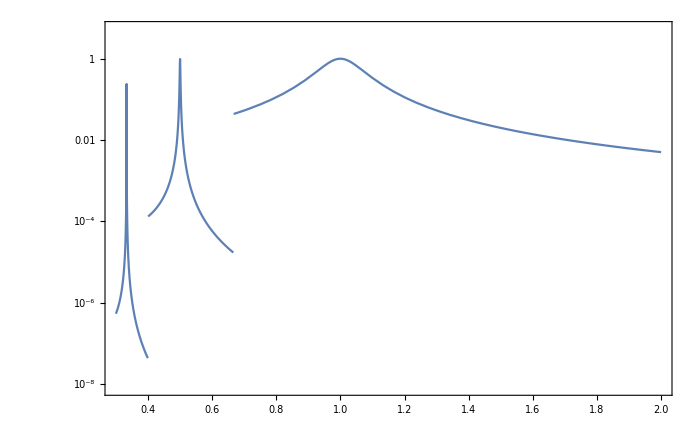

```mathematica
LogPlot[amplitude[k,0.1,Pi/5],{k,0.3,2},ImageSize->imgsize,Frame->True,PlotRange->Full]
```

```mathematica
Series[BesselJ[0,x],{x,0,3}]
```

1-x^2/4+O[x]^4

```mathematica
Limit[BesselJ[0,x]/x,x->0]
```

∞